# Pango analysis: Plotting partitioned case counts and Rt

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/trvrb/Documents/src/rt-from-frequency-dynamics/results/pango-countries

```mathematica
dataset="pango-countries";
```

```mathematica
model="GARW";
```

```mathematica
imageSize=300;
```

```mathematica
gridCount=1;
```

## Setup

### Date ticks

```mathematica
dateTicks={"2021-10-01","2021-11-01","2021-12-01","2022-01-01","2022-02-01","2022-03-01","2022-04-01","2022-05-01","2022-06-01","2022-07-01","2022-08-01","2022-09-01","2022-10-01","2022-11-01","2022-12-01"};
```

### Countries

```mathematica
countriesToDrop={};
```

## Variants and colors

### Import

```mathematica
variantData=Import["../../estimates/"<>dataset<>"/"<>dataset<>"_Rt-combined-"<>model<>".tsv"];
```

```mathematica
header=variantData[[1]]
```

{date,location,variant,median_R,R_upper_95,R_lower_95,R_upper_80,R_lower_80,R_upper_50,R_lower_50,median_freq}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_R→4,R_upper_95→5,R_lower_95→6,R_upper_80→7,R_lower_80→8,R_upper_50→9,R_lower_50→10,median_freq→11}

```mathematica
variantData=Drop[variantData,1];
```

```mathematica
variants=Union[variantData[[All,3]]]
```

{BA.2.3.20,BA.2.75,BA.2.75.2,BA.4.6,BA.4.6.5,BA.5,BA.5.1,BA.5.1.1,BA.5.1.10,BA.5.1.12,BA.5.1.18,BA.5.1.22,BA.5.1.23,BA.5.1.27,BA.5.1.30,BA.5.1.5,BA.5.1.6,BA.5.2,BA.5.2.1,BA.5.2.13,BA.5.2.16,BA.5.2.20,BA.5.2.21,BA.5.2.23,BA.5.2.34,BA.5.2.35,BA.5.2.6,BA.5.2.9,BA.5.3.1,BA.5.5,BA.5.5.1,BA.5.6,BA.5.9,BE.1,BE.1.1,BE.1.1.1,BE.1.2.1,BE.1.4.2,BE.4,BF.10,BF.11,BF.13,BF.14,BF.26,BF.32,BF.5,BF.7,BF.7.4,BF.7.4.1,BF.7.5,BN.1,BN.1.3,BN.1.3.1,BN.1.5,BQ.1,BQ.1.1,BQ.1.10,BQ.1.10.1,BQ.1.11,BQ.1.1.18,BQ.1.12,BQ.1.1.3,BQ.1.13,BQ.1.1.4,BQ.1.14,BQ.1.1.5,BQ.1.1.7,BQ.1.2,BQ.1.22,BQ.1.23,BQ.1.3,BQ.1.5,BQ.1.6,CK.1,CQ.2,CR.1.1,other,XBB.1,XBB.2}

```mathematica
n=Length[variants]
```

79

### Max frequency

```mathematica
variantFrequencyMapping=Table[variant->Max[Cases[variantData,x_/;x[[3]]==variant][[All,11]]],{variant,variants}];
```

```mathematica
highFrequencyVariants=Cases[variantFrequencyMapping,x_/;x[[2]]>=0.005][[All,1]];
```

```mathematica
Length[highFrequencyVariants]
```

64

```mathematica
lowFrequencyVariants=Complement[variants,highFrequencyVariants];
```

```mathematica
Length[lowFrequencyVariants]
```

15

```mathematica
variants=Join[highFrequencyVariants,lowFrequencyVariants];
```

```mathematica
n=Length[variants]
```

79

### Variant to clade mapping and clade colors

```mathematica
toHexString[n_Integer]:=StringJoin[ToString/@(IntegerDigits[n,16]/.Thread[Range[10,15]->CharacterRange["A","F"]])]
```

```mathematica
rgbColorToHex[rgbColor_]:="#"<>StringJoin[Map[toHexString[Round[#*255]]&,Level[rgbColor,1]]]
```

```mathematica
start[n_]:=0.05;
```

```mathematica
stop[n_]:=0.99;
```

```mathematica
gap[n_]:=(stop[n]-start[n])/(n-1)
```

```mathematica
makeColors[n_]:=Table[ColorData["Rainbow"][i],{i,start[n],stop[n],gap[n]}];
```

```mathematica
startGrays[n_]:=0.35;
```

```mathematica
stopGrays[n_]:=0.65;
```

```mathematica
gapGrays[n_]:=(stopGrays[n]-startGrays[n])/(n-1)
```

```mathematica
makeGrays[n_]:=Table[GrayLevel[i],{i,startGrays[n],stopGrays[n],gapGrays[n]}];
```

```mathematica
variantToClade=Map[#[[1]]->#[[2]]&,Drop[Import["../../data/pango-countries/pango_aliasing.tsv"],1]];
```

```mathematica
clades={"other","21L (Omicron)","22A (Omicron)","22B (Omicron)","22C (Omicron)","22D (Omicron)","22E (Omicron)","22F (Omicron)"};
```

```mathematica
cladeColors=Prepend[makeColors[Length[clades]-1],Gray]
```

{GrayLevel[0.5],RGBColor[0.3431304, 0.11581720000000001, 0.6369784000000001],RGBColor[0.2508395466666667, 0.39970474666666667, 0.8119271333333333],RGBColor[0.35029528, 0.6426579866666666, 0.6632338133333334],RGBColor[0.54357188, 0.73433536, 0.41441192],RGBColor[0.7790337599999999, 0.7248730533333333, 0.26747425333333336],RGBColor[0.901627, 0.5398720000000001, 0.20836600000000002],RGBColor[0.86067868, 0.15704232000000004, 0.13666448]}

```mathematica
cladeToColor=MapThread[#1->#2&,{clades,cladeColors}]
```

{other→GrayLevel[0.5],21L (Omicron)→RGBColor[0.3431304, 0.11581720000000001, 0.6369784000000001],22A (Omicron)→RGBColor[0.2508395466666667, 0.39970474666666667, 0.8119271333333333],22B (Omicron)→RGBColor[0.35029528, 0.6426579866666666, 0.6632338133333334],22C (Omicron)→RGBColor[0.54357188, 0.73433536, 0.41441192],22D (Omicron)→RGBColor[0.7790337599999999, 0.7248730533333333, 0.26747425333333336],22E (Omicron)→RGBColor[0.901627, 0.5398720000000001, 0.20836600000000002],22F (Omicron)→RGBColor[0.86067868, 0.15704232000000004, 0.13666448]}

### Colors

```mathematica
colorMappingForClade[clade_]:=Module[{pos,shades,tints,col},
pos=Flatten[Position[variants,x_/;(x/.variantToClade)==clade]];
If[Length[pos]>0,
shades=Reverse[Table[Darker[clade/.cladeToColor,x],{x,0,0.5,1/(Length[pos])}]];
tints=Drop[Table[Lighter[clade/.cladeToColor,x],{x,0,0.5,1/(Length[pos])}],1];
col=Join[shades,tints];
Table[variants[[pos[[i]]]]->col[[i]],{i,Length[pos]}],
{}
]
]
```

```mathematica
variantColorMapping=Flatten[Map[colorMappingForClade,clades]]
```

{other→RGBColor[0.5, 0.5, 0.5],BA.2.3.20→RGBColor[0.3431304, 0.11581720000000001, 0.6369784000000001],BA.4.6→RGBColor[0.12541977333333335, 0.19985237333333333, 0.40596356666666666],BA.4.6.5→RGBColor[0.2508395466666667, 0.39970474666666667, 0.8119271333333333],BA.5→RGBColor[0.17514764, 0.3213289933333333, 0.3316169066666667],BA.5.1→RGBColor[0.1824454583333333, 0.33471770138888884, 0.3454342777777778],BA.5.1.1→RGBColor[0.18974327666666665, 0.34810640944444443, 0.35925164888888894],BA.5.1.10→RGBColor[0.197041095, 0.36149511749999996, 0.37306902000000003],BA.5.1.18→RGBColor[0.20433891333333332, 0.3748838255555555, 0.38688639111111117],BA.5.1.22→RGBColor[0.21163673166666666, 0.3882725336111111, 0.4007037622222223],BA.5.1.23→RGBColor[0.21893455, 0.4016612416666666, 0.4145211333333334],BA.5.1.27→RGBColor[0.22623236833333332, 0.4150499497222222, 0.4283385044444445],BA.5.1.30→RGBColor[0.23353018666666667, 0.4284386577777778, 0.44215587555555563],BA.5.1.5→RGBColor[0.24082800499999998, 0.4418273658333333, 0.4559732466666667],BA.5.2→RGBColor[0.24812582333333333, 0.45521607388888885, 0.46979061777777786],BA.5.2.1→RGBColor[0.25542364166666665, 0.46860478194444444, 0.483607988888889],BA.5.2.20→RGBColor[0.26272145999999996, 0.48199348999999997, 0.49742536000000004],BA.5.2.21→RGBColor[0.27001927833333333, 0.4953821980555555, 0.5112427311111112],BA.5.2.23→RGBColor[0.27731709666666665, 0.5087709061111111, 0.5250601022222223],BA.5.2.34→RGBColor[0.284614915, 0.5221596141666667, 0.5388774733333335],BA.5.2.35→RGBColor[0.29191273333333334, 0.5355483222222222, 0.5526948444444445],BA.5.2.6→RGBColor[0.29921055166666666, 0.5489370302777777, 0.5665122155555556],BA.5.2.9→RGBColor[0.30650837, 0.5623257383333333, 0.5803295866666668],BA.5.3.1→RGBColor[0.3138061883333333, 0.5757144463888888, 0.5941469577777778],BA.5.5→RGBColor[0.32110400666666666, 0.5891031544444444, 0.607964328888889],BA.5.5.1→RGBColor[0.328401825, 0.6024918625, 0.6217817000000001],BA.5.6→RGBColor[0.3356996433333333, 0.6158805705555556, 0.6355990711111112],BE.1→RGBColor[0.34299746166666667, 0.629269278611111, 0.6494164422222223],BE.1.1→RGBColor[0.35029528, 0.6426579866666666, 0.6632338133333334],BF.10→RGBColor[0.363830795, 0.6501026119444444, 0.6702497755555556],BF.11→RGBColor[0.37736631, 0.6575472372222222, 0.6772657377777779],BF.13→RGBColor[0.390901825, 0.6649918625, 0.6842817000000001],BF.26→RGBColor[0.40443734, 0.6724364877777778, 0.6912976622222223],BF.5→RGBColor[0.417972855, 0.6798811130555555, 0.6983136244444446],BF.7→RGBColor[0.43150837, 0.6873257383333333, 0.7053295866666668],BF.7.4→RGBColor[0.44504388500000003, 0.6947703636111111, 0.712345548888889],BF.7.4.1→RGBColor[0.45857939999999997, 0.7022149888888889, 0.7193615111111111],CK.1→RGBColor[0.472114915, 0.7096596141666667, 0.7263774733333335],CQ.2→RGBColor[0.48565042999999997, 0.7171042394444445, 0.7333934355555556],CR.1.1→RGBColor[0.499185945, 0.7245488647222222, 0.7404093977777778],BA.5.1.12→RGBColor[0.51272146, 0.73199349, 0.74742536],BA.5.1.6→RGBColor[0.526256975, 0.7394381152777777, 0.7544413222222223],BA.5.2.13→RGBColor[0.53979249, 0.7468827405555556, 0.7614572844444445],BA.5.2.16→RGBColor[0.553328005, 0.7543273658333333, 0.7684732466666667],BA.5.9→RGBColor[0.56686352, 0.761771991111111, 0.775489208888889],BE.1.1.1→RGBColor[0.580399035, 0.7692166163888888, 0.7825051711111112],BE.1.2.1→RGBColor[0.59393455, 0.7766612416666666, 0.7895211333333334],BE.1.4.2→RGBColor[0.607470065, 0.7841058669444444, 0.7965370955555556],BE.4→RGBColor[0.6210055800000001, 0.7915504922222222, 0.8035530577777779],BF.14→RGBColor[0.634541095, 0.7989951175, 0.8105690200000001],BF.32→RGBColor[0.6480766099999999, 0.8064397427777777, 0.8175849822222223],BF.7.5→RGBColor[0.661612125, 0.8138843680555555, 0.8246009444444444],BA.2.75→RGBColor[0.38951687999999995, 0.36243652666666665, 0.13373712666666668],BN.1→RGBColor[0.51935584, 0.4832487022222222, 0.1783161688888889],BN.1.3→RGBColor[0.6491948, 0.6040608777777777, 0.22289521111111113],BN.1.3.1→RGBColor[0.7790337599999999, 0.7248730533333333, 0.26747425333333336],BA.2.75.2→RGBColor[0.8158614666666666, 0.7707275444444444, 0.3895618777777778],BN.1.5→RGBColor[0.8526891733333333, 0.8165820355555555, 0.5116495022222223],BQ.1→RGBColor[0.47454052631578947, 0.28414315789473693, 0.10966631578947371],BQ.1.1→RGBColor[0.5219945789473683, 0.3125574736842106, 0.12063294736842108],BQ.1.10→RGBColor[0.5694486315789473, 0.34097178947368434, 0.13159957894736846],BQ.1.10.1→RGBColor[0.6169026842105263, 0.36938610526315796, 0.1425662105263158],BQ.1.11→RGBColor[0.6643567368421053, 0.3978004210526317, 0.1535328421052632],BQ.1.1.18→RGBColor[0.7118107894736841, 0.42621473684210537, 0.16449947368421056],BQ.1.12→RGBColor[0.7592648421052631, 0.45462905263157904, 0.17546610526315792],BQ.1.1.3→RGBColor[0.8067188947368421, 0.4830433684210528, 0.1864327368421053],BQ.1.13→RGBColor[0.854172947368421, 0.5114576842105264, 0.19739936842105266],BQ.1.1.4→RGBColor[0.901627, 0.5398720000000001, 0.20836600000000002],BQ.1.14→RGBColor[0.9068045263157894, 0.5640892631578949, 0.2500309473684211],BQ.1.1.5→RGBColor[0.9119820526315789, 0.5883065263157896, 0.2916958947368421],BQ.1.1.7→RGBColor[0.9171595789473684, 0.6125237894736844, 0.3333608421052632],BQ.1.2→RGBColor[0.9223371052631578, 0.6367410526315791, 0.3750257894736842],BQ.1.22→RGBColor[0.9275146315789473, 0.6609583157894737, 0.4166907368421052],BQ.1.23→RGBColor[0.9326921578947368, 0.6851755789473685, 0.4583556842105263],BQ.1.3→RGBColor[0.9378696842105263, 0.7093928421052632, 0.5000206315789474],BQ.1.5→RGBColor[0.9430472105263158, 0.733610105263158, 0.5416855789473684],BQ.1.6→RGBColor[0.9482247368421053, 0.7578273684210527, 0.5833505263157894],XBB.1→RGBColor[0.43033934, 0.07852116000000002, 0.06833224],XBB.2→RGBColor[0.86067868, 0.15704232000000004, 0.13666448]}

```mathematica
highFrequencyColors=highFrequencyVariants/.variantColorMapping
```

{RGBColor[0.3431304, 0.11581720000000001, 0.6369784000000001],RGBColor[0.38951687999999995, 0.36243652666666665, 0.13373712666666668],RGBColor[0.12541977333333335, 0.19985237333333333, 0.40596356666666666],RGBColor[0.2508395466666667, 0.39970474666666667, 0.8119271333333333],RGBColor[0.17514764, 0.3213289933333333, 0.3316169066666667],RGBColor[0.1824454583333333, 0.33471770138888884, 0.3454342777777778],RGBColor[0.18974327666666665, 0.34810640944444443, 0.35925164888888894],RGBColor[0.197041095, 0.36149511749999996, 0.37306902000000003],RGBColor[0.20433891333333332, 0.3748838255555555, 0.38688639111111117],RGBColor[0.21163673166666666, 0.3882725336111111, 0.4007037622222223],RGBColor[0.21893455, 0.4016612416666666, 0.4145211333333334],RGBColor[0.22623236833333332, 0.4150499497222222, 0.4283385044444445],RGBColor[0.23353018666666667, 0.4284386577777778, 0.44215587555555563],RGBColor[0.24082800499999998, 0.4418273658333333, 0.4559732466666667],RGBColor[0.24812582333333333, 0.45521607388888885, 0.46979061777777786],RGBColor[0.25542364166666665, 0.46860478194444444, 0.483607988888889],RGBColor[0.26272145999999996, 0.48199348999999997, 0.49742536000000004],RGBColor[0.27001927833333333, 0.4953821980555555, 0.5112427311111112],RGBColor[0.27731709666666665, 0.5087709061111111, 0.5250601022222223],RGBColor[0.284614915, 0.5221596141666667, 0.5388774733333335],RGBColor[0.29191273333333334, 0.5355483222222222, 0.5526948444444445],RGBColor[0.29921055166666666, 0.5489370302777777, 0.5665122155555556],RGBColor[0.30650837, 0.5623257383333333, 0.5803295866666668],RGBColor[0.3138061883333333, 0.5757144463888888, 0.5941469577777778],RGBColor[0.32110400666666666, 0.5891031544444444, 0.607964328888889],RGBColor[0.328401825, 0.6024918625, 0.6217817000000001],RGBColor[0.3356996433333333, 0.6158805705555556, 0.6355990711111112],RGBColor[0.34299746166666667, 0.629269278611111, 0.6494164422222223],RGBColor[0.35029528, 0.6426579866666666, 0.6632338133333334],RGBColor[0.363830795, 0.6501026119444444, 0.6702497755555556],RGBColor[0.37736631, 0.6575472372222222, 0.6772657377777779],RGBColor[0.390901825, 0.6649918625, 0.6842817000000001],RGBColor[0.40443734, 0.6724364877777778, 0.6912976622222223],RGBColor[0.417972855, 0.6798811130555555, 0.6983136244444446],RGBColor[0.43150837, 0.6873257383333333, 0.7053295866666668],RGBColor[0.44504388500000003, 0.6947703636111111, 0.712345548888889],RGBColor[0.45857939999999997, 0.7022149888888889, 0.7193615111111111],RGBColor[0.51935584, 0.4832487022222222, 0.1783161688888889],RGBColor[0.6491948, 0.6040608777777777, 0.22289521111111113],RGBColor[0.7790337599999999, 0.7248730533333333, 0.26747425333333336],RGBColor[0.47454052631578947, 0.28414315789473693, 0.10966631578947371],RGBColor[0.5219945789473683, 0.3125574736842106, 0.12063294736842108],RGBColor[0.5694486315789473, 0.34097178947368434, 0.13159957894736846],RGBColor[0.6169026842105263, 0.36938610526315796, 0.1425662105263158],RGBColor[0.6643567368421053, 0.3978004210526317, 0.1535328421052632],RGBColor[0.7118107894736841, 0.42621473684210537, 0.16449947368421056],RGBColor[0.7592648421052631, 0.45462905263157904, 0.17546610526315792],RGBColor[0.8067188947368421, 0.4830433684210528, 0.1864327368421053],RGBColor[0.854172947368421, 0.5114576842105264, 0.19739936842105266],RGBColor[0.901627, 0.5398720000000001, 0.20836600000000002],RGBColor[0.9068045263157894, 0.5640892631578949, 0.2500309473684211],RGBColor[0.9119820526315789, 0.5883065263157896, 0.2916958947368421],RGBColor[0.9171595789473684, 0.6125237894736844, 0.3333608421052632],RGBColor[0.9223371052631578, 0.6367410526315791, 0.3750257894736842],RGBColor[0.9275146315789473, 0.6609583157894737, 0.4166907368421052],RGBColor[0.9326921578947368, 0.6851755789473685, 0.4583556842105263],RGBColor[0.9378696842105263, 0.7093928421052632, 0.5000206315789474],RGBColor[0.9430472105263158, 0.733610105263158, 0.5416855789473684],RGBColor[0.472114915, 0.7096596141666667, 0.7263774733333335],RGBColor[0.48565042999999997, 0.7171042394444445, 0.7333934355555556],RGBColor[0.499185945, 0.7245488647222222, 0.7404093977777778],RGBColor[0.5, 0.5, 0.5],RGBColor[0.43033934, 0.07852116000000002, 0.06833224],RGBColor[0.86067868, 0.15704232000000004, 0.13666448]}

```mathematica
lowFrequencyColors=makeGrays[Length[lowFrequencyVariants]]
```

{GrayLevel[0.35],GrayLevel[0.3714285714285714],GrayLevel[0.39285714285714285],GrayLevel[0.41428571428571426],GrayLevel[0.4357142857142857],GrayLevel[0.45714285714285713],GrayLevel[0.47857142857142854],GrayLevel[0.5],GrayLevel[0.5214285714285715],GrayLevel[0.5428571428571429],GrayLevel[0.5642857142857143],GrayLevel[0.5857142857142857],GrayLevel[0.6071428571428572],GrayLevel[0.6285714285714286],GrayLevel[0.65]}

```mathematica
colors=Join[highFrequencyColors,lowFrequencyColors];
```

```mathematica
legendPanel=PointLegend[highFrequencyColors,highFrequencyVariants,LabelStyle->Directive[FontSize->10],LegendMarkerSize->20,LegendLayout->{"Column",7},Spacings->{0,0.1}]
```

```mathematica
variantToColor=MapThread[#1->#2&,{variants,colors}];
```

```mathematica
variantToIndex=MapThread[#1->#2&,{variants,Range[n]}];
```

## Rt estimates

```mathematica
rtData=Import["../../estimates/"<>dataset<>"/"<>dataset<>"_Rt-combined-"<>model<>".tsv"];
```

```mathematica
header=rtData[[1]]
```

{date,location,variant,median_R,R_upper_95,R_lower_95,R_upper_80,R_lower_80,R_upper_50,R_lower_50,median_freq}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_R→4,R_upper_95→5,R_lower_95→6,R_upper_80→7,R_lower_80→8,R_upper_50→9,R_lower_50→10,median_freq→11}

```mathematica
rtData=Drop[rtData,1];
```

```mathematica
startDate=DateString[DatePlus[First[Sort[rtData[[All,1]]]],10],{"Year","-","Month", "-","Day"}]
```

2022-08-11

```mathematica
modelEndDate=Last[Sort[rtData[[All,1]]]]
```

2022-11-28

```mathematica
endDate=Last[Sort[rtData[[All,1]]]]
```

2022-11-28

```mathematica
dates=Table[DateString[DatePlus[startDate,d],{"Year","-","Month", "-","Day"}],{d,0,QuantityMagnitude[DateDifference[startDate,endDate]]}];
```

```mathematica
countries=Union[rtData[[All,2]]]
```

{USA}

```mathematica
countries=DeleteCases[countries,x_/;MemberQ[countriesToDrop,x]]
```

{USA}

Only keep Rt data points when the variant is frequent enough to have a good estimate

```mathematica
rtData=Cases[rtData,x_/;x[[11]]>0.005];
```

```mathematica
rtGather[country_,variant_]:=Cases[rtData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,4}]]
```

```mathematica
rtGatherLower[country_,variant_]:=Cases[rtData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,8}]]
```

```mathematica
rtGatherUpper[country_,variant_]:=Cases[rtData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,7}]]
```

```mathematica
variantCountryRtPlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=rtGather[country,variant];
lowerSeries=rtGatherLower[country,variant];
upperSeries=rtGatherUpper[country,variant];
DateListPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Rt"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{55,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{0.6,1.4}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],Dashed,Black,Line[{{startDate,1},{modelEndDate,1}}]}]
]
```

```mathematica
countryRtPlot[country_]:=Show[Table[variantCountryRtPlot[country,variants[[i]],colors[[i]]],{i,1,n}]]
```

```mathematica
rtPanels=Map[countryRtPlot,countries];
```

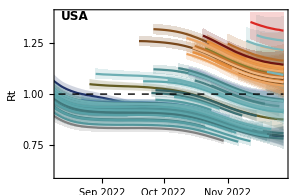
-Graphics- |

```mathematica
fig=Grid[{{countryRtPlot["USA"],legendPanel}},Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-rt.png",fig,"PNG",ImageResolution->300]
```

figures/pango-countries_variant-rt.png

```mathematica
finalRts=Table[If[Length[rtGather["USA",variant]]>0,rtGather["USA",variant][[-1,2]],Null],{variant,variants}];
```

```mathematica
finalRtsLower=Table[If[Length[rtGatherLower["USA",variant]]>0,rtGatherLower["USA",variant][[-1,2]],Null],{variant,variants}];
```

```mathematica
finalRtsUpper=Table[If[Length[rtGatherUpper["USA",variant]]>0,rtGatherUpper["USA",variant][[-1,2]],Null],{variant,variants}];
```

## Prevalence

```mathematica
pData=Import["../../estimates/"<>dataset<>"/"<>dataset<>"_I-combined-"<>model<>".tsv"];
```

```mathematica
header=pData[[1]]
```

{date,location,variant,median_I_smooth,I_smooth_upper_95,I_smooth_lower_95,I_smooth_upper_80,I_smooth_lower_80,I_smooth_upper_50,I_smooth_lower_50,median_freq}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_I_smooth→4,I_smooth_upper_95→5,I_smooth_lower_95→6,I_smooth_upper_80→7,I_smooth_lower_80→8,I_smooth_upper_50→9,I_smooth_lower_50→10,median_freq→11}

```mathematica
pData=Drop[pData,1];
```

Only keep data points with incidence

```mathematica
pData=Cases[pData,x_/;x[[4]]>0.9];
```

```mathematica
pGather[country_,variant_]:=Cases[pData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,4}]]
```

```mathematica
pGatherLower[country_,variant_]:=Cases[pData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,8}]]
```

```mathematica
pGatherUpper[country_,variant_]:=Cases[pData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,7}]]
```

```mathematica
variantCountryPrevalencePlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=pGather[country,variant];
lowerSeries=pGatherLower[country,variant];
upperSeries=pGatherUpper[country,variant];
DateListLogPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Estimated variant cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{55,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{200,100000}},DateTicksFormat->{"MonthNameShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{{10,20,100,200,1000,2000,10000,20000,100000,200000,1000000},Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]}]
]
```

```mathematica
countryPrevalencePlot[country_]:=Show[Table[variantCountryPrevalencePlot[country,variants[[i]],colors[[i]]],{i,1,n}]]
```

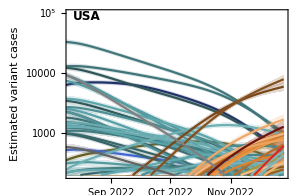
-Graphics- |

```mathematica
fig=Grid[{{countryPrevalencePlot["USA"],legendPanel}},Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-estimated-log-cases.png",fig,"PNG",ImageResolution->300]
```

figures/pango-countries_variant-estimated-log-cases.png

```mathematica
variantCountryPrevalencePlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=pGather[country,variant];
lowerSeries=pGatherLower[country,variant];
upperSeries=pGatherUpper[country,variant];
DateListPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Estimated variant cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{55,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{0,32000}},DateTicksFormat->{"MonthNameShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]}]
]
```

```mathematica
countryPrevalencePlot[country_]:=Show[Table[variantCountryPrevalencePlot[country,variants[[i]],colors[[i]]],{i,1,n}]]
```

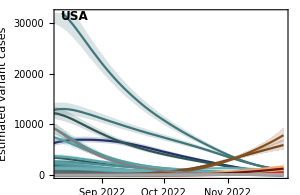
-Graphics- |

```mathematica
fig=Grid[{{countryPrevalencePlot["USA"],legendPanel}},Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-estimated-cases.png",fig,"PNG",ImageResolution->300]
```

figures/pango-countries_variant-estimated-cases.png

## Frequency

```mathematica
logitTransform[x_]:=Log[x/(1-x)]
```

```mathematica
logitBackTransform[y_]:=Exp[y]/(1+ Exp[y])
```

```mathematica
logitTicks=Map[{logitTransform[#],ToString[If[#<0.01,NumberForm[Round[100*#,0.1],{3,1}],Round[100*#]]]<>"%"}&,{0.001,0.01,0.1,0.5,0.9,0.99}];
```

```mathematica
fData=Import["../../estimates/"<>dataset<>"/"<>dataset<>"_freq-combined-"<>model<>".tsv"];
```

```mathematica
header=fData[[1]]
```

{date,location,variant,median_freq,freq_upper_95,freq_lower_95,freq_upper_80,freq_lower_80,freq_upper_50,freq_lower_50}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_freq→4,freq_upper_95→5,freq_lower_95→6,freq_upper_80→7,freq_lower_80→8,freq_upper_50→9,freq_lower_50→10}

```mathematica
fData=Drop[fData,1];
```

```mathematica
fGather[country_,variant_]:=Cases[fData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,4}]]
```

```mathematica
fGatherLower[country_,variant_]:=Cases[fData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,8}]]
```

```mathematica
fGatherUpper[country_,variant_]:=Cases[fData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,7}]]
```

```mathematica
logitTransformDateSeries[dateSeries_]:=Map[{#[[1]],Which[#[[2]]<0.0001,logitTransform[0.0001],#[[2]]>0.9999,logitTransform[0.9999],True,logitTransform[#[[2]]]]}&,dateSeries]
```

```mathematica
variantCountryFrequencyPlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=logitTransformDateSeries[fGather[country,variant]];
lowerSeries=logitTransformDateSeries[fGatherLower[country,variant]];
upperSeries=logitTransformDateSeries[fGatherUpper[country,variant]];
DateListPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Estimated variant frequency"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{55,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{logitTransform[0.0005],logitTransform[0.9]}},DateTicksFormat->{"MonthNameShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{logitTicks,Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]}]
]
```

```mathematica
countryFrequencyPlot[country_]:=Show[Table[variantCountryFrequencyPlot[country,variants[[i]],colors[[i]]],{i,1,n}]]
```

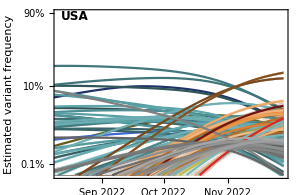
-Graphics- |

```mathematica
fig=Grid[{{countryFrequencyPlot["USA"],legendPanel}},Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-estimated-frequency.png",fig,"PNG",ImageResolution->300]
```

figures/pango-countries_variant-estimated-frequency.png

```mathematica
finalFrequencies=Table[fGather["USA",variant][[-1,2]],{variant,variants}];
```

## Rts and frequencies across variants

```mathematica
pos=Flatten[Position[finalRts,x_/;NumberQ[x]]];
```

```mathematica
finalRts=finalRts[[pos]];
```

```mathematica
finalRtsLower=finalRtsLower[[pos]];
```

```mathematica
finalRtsUpper=finalRtsUpper[[pos]];
```

```mathematica
finalFrequencies=finalFrequencies[[pos]];
```

```mathematica
finalVariants=variants[[pos]];
```

```mathematica
finalColors=colors[[pos]];
```

```mathematica
points=ListPlot[Table[{{i,finalRts[[i]]}},{i,Length[finalVariants]}],PlotStyle->finalColors];
```

```mathematica
lines=ListLinePlot[Table[{{i,finalRtsLower[[i]]},{i,finalRtsUpper[[i]]}},{i,Length[finalVariants]}],PlotTheme->"FullAxes",Frame->{True,True,False,False},FrameLabel->{"","Rt"},PlotStyle->Map[Directive[Opacity[0.75],#]&,finalColors],AspectRatio->0.35,ImageSize->600,PlotRange->{0.7,1.4},FrameTicks->{{Automatic,Automatic},{Table[{i,Rotate[finalVariants[[i]],Pi/2]},{i,Length[finalVariants]}],Automatic}},Epilog->{Text[Style["USA",Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],Dashed,Black,Line[{{0,1},{n,1}}]}];
```

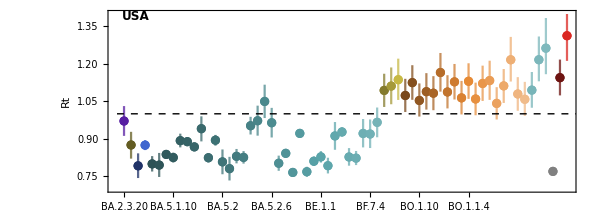

```mathematica
fig=Show[lines,points]
```

```mathematica
Export["figures/"<>dataset<>"_variant-rt-listplot.png",fig,"PNG",ImageResolution->300]
```

figures/pango-countries_variant-rt-listplot.png

```mathematica
topPos=Reverse[Ordering[finalRts,-8]];
```

```mathematica
tableValues=Table[{finalVariants[[p]],Round[finalRts[[p]],0.01],ToString[Round[finalRtsLower[[p]],0.01]]<>" - "<>ToString[Round[finalRtsUpper[[p]],0.01]]},{p,topPos}];
```

```mathematica
table=Style[TableForm[tableValues,TableHeadings->{None,{"lineage","Rt estimate","80% uncertainty interval"}},TableSpacing->{3,1}],FontFamily->"Helvetica",FontSize->12];
```

```mathematica
labels=Table[If[MemberQ[topPos,i],finalVariants[[i]],""],{i,Length[finalRts]}];
```

```mathematica
points=ListPlot[MapThread[{{#1,#2}}&,{finalFrequencies,finalRts}],PlotTheme->"FullAxes",Frame->{True,True,False,False},FrameLabel->{"Current lineage frequency","Rt"},PlotStyle->Map[Directive[Opacity[0.75],#]&,finalColors],AspectRatio->0.65,ImageSize->350,PlotRange->{{0,0.23},{0.7,1.4}},FrameTicks->{{Automatic,Automatic},{Table[{i,ToString[Round[100*i]]<>"%"},{i,0,1,0.05}],Automatic}},Epilog->{Text[Style["USA",Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],Dashed,Black,Line[{{0,1},{n,1}}]},PlotLabels->Placed[labels,Right]];
```

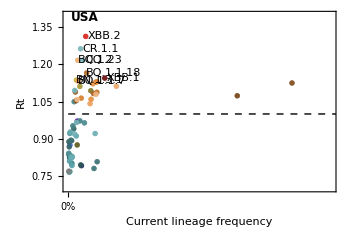
-Graphics- | lineage | Rt estimate | 80% uncertainty interval
XBB.2 | 1.31 | 1.21 - 1.42
CR.1.1 | 1.26 | 1.16 - 1.38
CQ.2 | 1.22 | 1.13 - 1.31
BQ.1.23 | 1.22 | 1.13 - 1.31
BQ.1.1.18 | 1.17 | 1.09 - 1.24
XBB.1 | 1.14 | 1.07 - 1.22
BN.1.3.1 | 1.14 | 1.06 - 1.22
BQ.1.1.7 | 1.13 | 1.06 - 1.21

```mathematica
fig=Grid[{{points,table}}]
```

```mathematica
Export["figures/"<>dataset<>"_variant-rt-top.png",fig,"PNG",ImageResolution->300]
```

figures/pango-countries_variant-rt-top.png